# Wavelength Physical Model

## by npk on April 21 2011 (See MOSFIRE DRP NB1 pg 28)

```mathematica
d=10^3/110.5
```

9.04977

```mathematica
d=10^3/110.5 ;(* groove spacing in µ *)
1/d
m=4;
mσ=m /d;
d=.;
```

0.1105

```mathematica
mσ
```

0.442

```mathematica
1/d
```

1/d

```mathematica
mσ
```

0.442

Physical Model

{a→1.00396,b→34.9365,c→1.,d→1.,e→1.}

2.27141 (0.609756+Sin[0.000071936 x])

δs---

-0.12332
0.209094
-0.0857739

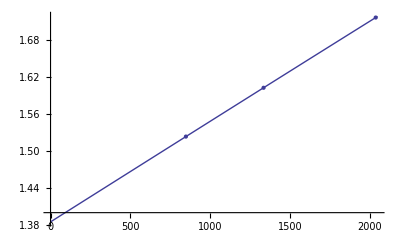

```mathematica
fun=a/mσ(Sin[ 17.984/(250 10^3)x ]+b °) +0(x-d)^3;
dat={{848, 1.52349}, {1334.5, 1.6027},{2037., 1.71666}};
{xdat,ydat}=Transpose[dat];
ff=FindFit[dat,fun,{{a,1},{b,180},c,d,e},x,MaxIterations->1000]
fun=fun/.ff
dff=D[fun,x];
Print["δs---"];Print[((fun/.x->xdat)-ydat )10000//TableForm]
Show[Plot[fun,{x,0, 2048}],ListPlot[dat]]
```

```mathematica
NSolve[fun==1.6027,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→722.441}}

1.45221+0.000162373 x

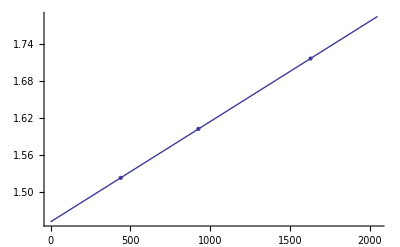

{0.874343,-1.47942,0.605075}

```mathematica
ff=Fit[dat,{1,x},x]
Show[ListPlot[dat],Plot[ff,{x,0,2048}]]
((ff/.x->xdat)-ydat)10000
```

33.6804+0.0252557 x

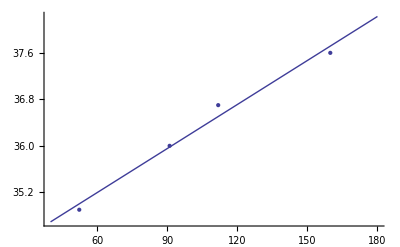

```mathematica
angs={{159.8, 37.6}, {111.8, 36.7}, {91, 36.0}, {52.3, 34.9}};
ff=Fit[angs,{1,x},x]
Show[ListPlot[angs],Plot[ff,{x,40,180}]]
```